```mathematica
ClearAll["Global`*"]
V0 = 1;
h = 1;
m = 1;
a = 5*Sqrt[2];
T[E_]:=If[E < V0,
(*E < V0*)(1+ (V0^2*Sinh[Sqrt[2*m*(V0-E)/h^2]*a]^2)/(4*E*(V0-E)))^(-1)
,
(*E > V0*)(1+ (V0^2*Sin[Sqrt[2*m*(E-V0)/h^2]*a]^2)/(4*E*(E-V0)))^(-1)
];
```

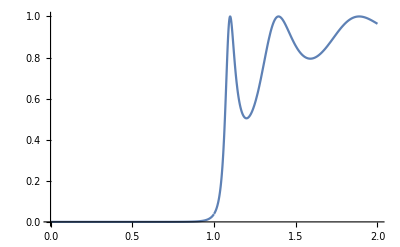

```mathematica
Plot[T[x], {x, 0, 2}]
```

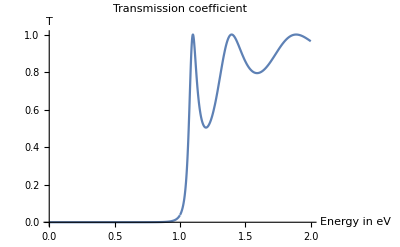

```mathematica
Show[%62,AxesLabel->{HoldForm[Energy in eV],HoldForm[T]},PlotLabel->HoldForm[Transmission coefficient],LabelStyle->{FontFamily->"Arial",10,GrayLevel[0]}]
```

```mathematica
Show[%63,ImageSize->Full]
```

-Graphics-

```mathematica
Show[%63,ImageSize->Large]
```

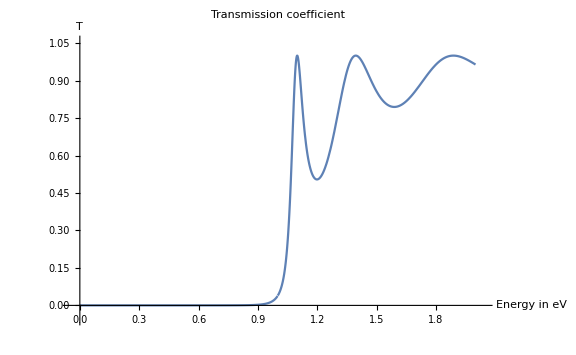

```mathematica
N[Exp[1+Pi*I]]
```

-2.71828

```mathematica
Fourier[{1, 2, 3, 4, 5, 6, 7, 8}]
```

{12.7279+0. ⅈ,-1.41421-3.41421 ⅈ,-1.41421-1.41421 ⅈ,-1.41421-0.585786 ⅈ,-1.41421+0. ⅈ,-1.41421+0.585786 ⅈ,-1.41421+1.41421 ⅈ,-1.41421+3.41421 ⅈ}